## Double Pendulum without Damping

The small angle approximation is not used, but we keep angles below about 60 degrees for now.

### Problem Description and geometry

A compound double pendulum is released from rest in a certain shape. It is then subject to gravity only, and friction is not modeled. We use the following values: 120 grams for mass, 20 centimeters for length, and 9.81 for g.

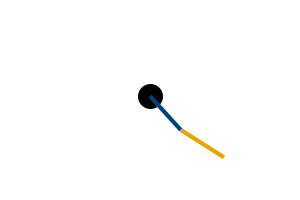

```mathematica
With[{L1=1,L2=1,m1=1,m2=1},Module[{pendulum1,pendulum2},
pendulum1=Line[{{0,0},{L1 Sin[θ1],-L1 Cos[θ1]}}]/.{θ1->30 Degree};
pendulum2=Line[{{L1 Sin[θ1],-L1 Cos[θ1]},{L1 Sin[θ1]+L2 Sin[θ2],-L1 Cos[θ1]-L2 Cos[θ2]}}]/.{θ1->30 Degree,θ2->45 Degree};
Graphics[
{
{PointSize[0.06],Point[{0,0}]},
{Thickness[0.01],ColorData[81,"ColorList"][[1]],pendulum1},
{Thickness[0.01],ColorData[81,"ColorList"][[2]],pendulum2}
},
PlotRange->{{-(L1+L2),(L1+L2)},{-1.1(L1+L2),(L1+L2)}},
Frame->False
,ImageSize->{300,200},ImagePadding->Automatic]]]
```

### Calculating and animating the solution

```mathematica
p1=Module[{eq1,eq2,T,V,Ξ1,Ξ2,v1,v2,r1,r2,L,sol,pendulum1,pendulum2,tfinal,max,min},
r1[θ1_,θ2_]:={L1/2 Sin[θ1],-L1/2 Cos[θ1]};
r2[θ1_,θ2_]:={L1 Sin[θ1]+L2/2 Sin[θ2],-L1 Cos[θ1]-L2/2 Cos[θ2]};
v1=D[r1[θ1[t],θ2[t]],t];
v2=D[r2[θ1[t],θ2[t]],t];
V=m1 g r1[θ1[t],θ2[t]][[2]]+m2 g r2[θ1[t],θ2[t]][[2]] ;(*m g y *)
T=1/2 m1 Dot[v1,v1]+1/2 m2 Dot[v2,v2];
Ξ1=-c θ1'[t];
Ξ2=-c θ2'[t];
L=T-V;
eq1=D[D[L,θ1'[t]],t]-D[L,θ1[t]]==0;
eq2=D[D[L,θ2'[t]],t]-D[L,θ2[t]]==0;
tfinal=5;
sol=With[{rules={g->9.81}},ParametricNDSolve[{eq1/.rules,eq2/.rules,θ1[0]==θ10,θ2[0]==θ20,θ1'[0]==0,θ2'[0]==0},{θ1,θ2,θ1',θ2'},{t,0,tfinal},{L1,m1,L2,m2,θ10,θ20}]];
Manipulate[With[{m1=0.12,m2=0.12(*,θ10=0.25π,θ20=0.25π*),θmax=90,θmin=-90},
Column@{Animate[Row@{Show[ParametricPlot[
{
{1/Degree θ1[L1,m1,L2,m2,θ10,θ20][t]/.sol,θ1'[L1,m1,L2,m2,θ10,θ20][t]/.sol},
{1/Degree θ2[L1,m1,L2,m2,θ10,θ20][t]/.sol,θ2'[L1,m1,L2,m2,θ10,θ20][t]/.sol}
},{t,0,tshowfinal},
PlotLegends->Placed[(Style[#,FontSize->16]&/@{"1","2"}),{0.1,0.1}],
PlotRange->{{θmin,θmax},{-15,15}},
Ticks->{Range[θmin,θmax,30],Automatic},
GridLines->{Range[θmin,θmax,30],Automatic},
PlotStyle->ColorData[81,"ColorList"],
PlotStyle->Thickness[0.005],
AspectRatio->1/2,
PlotLabel->Style["Phase portrait",FontSize->16],
AxesLabel->(Style[#,FontSize->16]&/@{"θ","θ̇"}),
PlotPoints->100,Epilog->Text["Time is "<>ToString@tshowfinal,{-800,10}],
ImageSize->{600,400}],
ListPlot[
{
{{1/Degree θ1[L1,m1,L2,m2,θ10,θ20][t],θ1'[L1,m1,L2,m2,θ10,θ20][t]}/.sol/.t->tshowfinal},
{{1/Degree θ2[L1,m1,L2,m2,θ10,θ20][t],θ2'[L1,m1,L2,m2,θ10,θ20][t]}/.sol/.t->tshowfinal}
},
PlotStyle->ColorData[81,"ColorList"]
]
],
Module[{},
pendulum1=Line[{{0,0},{L1 Sin[θ1],-L1 Cos[θ1]}}]/.{θ1->θ1[L1,m1,L2,m2,θ10,θ20][t]}/.sol;
pendulum2=Line[{{L1 Sin[θ1],-L1 Cos[θ1]},{L1 Sin[θ1]+L2 Sin[θ2],-L1 Cos[θ1]-L2 Cos[θ2]}}]/.{θ1->θ1[L1,m1,L2,m2,θ10,θ20][t],θ2->θ2[L1,m1,L2,m2,θ10,θ20][t]}/.sol;
Graphics[
{
{PointSize[0.01],Point[{0,0}]},
{Thickness[0.01],ColorData[81,"ColorList"][[1]],pendulum1},
{Thickness[0.01],ColorData[81,"ColorList"][[2]],pendulum2}
}/.t->tshowfinal,
PlotRange->{{-(L1+L2),(L1+L2)},{-(L1+L2),0.1}},
Frame->False
,ImageSize->{300,200}]]
},
{{tshowfinal,0.01,"Time "},0.01,tfinal},AnimationRepetitions->1,AnimationRate->0.5],Plot[{1/Degree θ1[L1,m1,L2,m2,θ10,θ20][t]/.sol,1/Degree θ2[L1,m1,L2,m2,θ10,θ20][t]/.sol},{t,0,tfinal},
ImageSize->{900,200},
PlotRange->{All,{-90,90}},
PlotLabel->Style["Time Evolution of θ_1 and θ_2",FontSize->16],
Ticks->{Automatic,Range[-90,90,30]},
GridLines->{Automatic,Range[-90,90,30]},
PlotPoints->60,
PlotStyle->ColorData[81,"ColorList"],
PlotLegends->Placed[(Style[#,FontSize->16]&/@{"θ_1","θ_2"}),{0.1,0.85}],
AspectRatio->Full]}
],{{θ10,30 Degree,Style["Initial Angle of Pendulum 1",FontSize->16]},0,45 Degree,5 Degree},
{{θ20,15 Degree,Style["Initial Angle of Pendulum 2",FontSize->16]},0,45 Degree,5Degree},
{{L1,0.20,Style["Length of Pendulum 1",FontSize->16]},0.05,0.4,0.05},
{{L2,0.20,Style["Length of Pendulum 2",FontSize->16]},0.05,0.4,0.05}
]
]
```

### Cloud Deployment

The URL is here: https://www.wolframcloud.com/obj/86f4b7c4-4bca-4acb-aec9-c9a2a8cb5d03 and here: ["https://www.wolframcloud.com/obj/eb3b76f0-c510-4018-8cad-a45e8f96b50e"](https://www.wolframcloud.com/obj/eb3b76f0-c510-4018-8cad-a45e8f96b50e)

```mathematica
(*CloudPublish[]*)
```

CloudObject[https://www.wolframcloud.com/obj/86f4b7c4-4bca-4acb-aec9-c9a2a8cb5d03]

```mathematica
(*CloudDeploy[p1,Permissions->"Public"]*)
```

CloudObject[https://www.wolframcloud.com/obj/eb3b76f0-c510-4018-8cad-a45e8f96b50e]